# Figuring out ∂Vi/∂Vk

This document creates an equation for the partial derivative of the traits in species i at time t+1 ((V̂)_i) with respect to the traits in species k at time t (V_j).

(V̂)_i = V_i + σ^2 [ 2 g V_i e^(-V_i*V_i^T) ( N_i + N_k e^(-d V_k*V_k^T) + (∑^n)_(j≠i,j≠k)N_j e^(-d V_j*V_j^T))-f V_i*(C+C^T)]

## Below is a configuration of traits and abundances for testing:

```mathematica
zVi={3.23531713336706,1.02777096442878,0.2787772170268};
zVk = {5.27526782592759,1.44656382501125,0.14410174684599};
zVnei={{9.97409204719588,1.06037032557651,2.78145811287686},
{5.59907909948379,2.24725058535114,1.8701455486007}};
zNi=9.4145709397;
zNk=7.34398103217961;
zNnei={19.0046921810612,10.0717215593192};
zf=0.2484041452;
zg=0.1476385485;
zCC={{1,-0.0450021495231871,-0.0450021495231871},
{-0.0450021495231871,1,-0.0450021495231871},
{-0.0450021495231871,-0.0450021495231871,1}};
zr0=0.4257492712;
zd=-0.0917747103;
zn = Length[zVnei] + 2;
zsigma2 = 0.1;
(* These are used as intermediate objects for some functions: *)
zCCC = (zCC+Transpose[zCC]);
zZ =∑_j^(-2+zn) ⅇ^(-zd zVneij.zVneij) zNneij;
```

### Function to compute new trait values based on old ones:

```mathematica
newV[Vi_,Vk_, Vnei_,Ni_,Nk_, Nnei_,f_,g_,CCC_,r0_,d_,n_,sigma2_]:= Vi + sigma2 * (2 * g * Vi * Exp[- Vi.Vi]* (
Ni +
Nk * Exp[-d * Vk.Vk]+
	Sum[
	Indexed[Nnei, j] * Exp[-d * Indexed[Vnei, j].Indexed[Vnei, j]],
	{j, n-2}
	]
)- 
f * Vi.CCC
)
newV[zVi,zVk, zVnei,zNi,zNk, zNnei,zf,zg,zCCC,zr0,zd,zn,zsigma2]
```

{3.42381,1.09458,0.304299}

```mathematica
newV[Vi_,Vk_, Ni_,Nk_, Z_, f_,g_,d_,CCC_,sigma2_]:= Vi + sigma2 * (2 * g * Vi * Exp[- Vi.Vi]* (Ni +Nk * Exp[-d * Vk.Vk]+Z)- 
f * Vi.CCC
)
newV[zVi,zVk, zNi,zNk, zZ,zf,zg, zd, zCCC,zsigma2]
```

{3.42381,1.09458,0.304299}

### And doing the same thing but using an expression that’s been simplified to use `Z` instead of the big summation section:

```mathematica
newVexpr:= Vi + sigma2 * ( 
2 * g * Vi * Exp[- Vi.Vi]*(Ni+Nk * Exp[-d * Vk.Vk]+Z)- 
f * Vi.CCC
)
newVexpr /. {Vi->zVi,Vk -> zVk, Ni -> zNi, Nk -> zNk,f->zf,g->zg,d -> zd,CCC->zCCC, sigma2 -> zsigma2, Z -> zZ}
```

{3.42381,1.09458,0.304299}

## Differentiating

### We can see below that we now have the same problem as before (creating ∂F/∂Vi) where Mathematica doesn’t handle matrices well:

```mathematica
D[newVexpr, {Vk}]
D[newVexpr, {Vi}]  /. {Vi->zVi,Vk -> zVk, Ni -> zNi, Nk -> zNk,f->zf,g->zg,d -> zd,CCC->zCCC, sigma2 -> zsigma2, Z -> zZ}
```

-2 d ⅇ^(-Vi.Vi-d Vk.Vk) g Nk sigma2 Vi (1.Vk+Vk.1)

{1+0.1 (1.07039-0.248404 1.{{2,-0.0900043,-0.0900043},{-0.0900043,2,-0.0900043},{-0.0900043,-0.0900043,2}}+3.46306 (-1.{3.23532,1.02777,0.278777}-{3.23532,1.02777,0.278777}.1)),1+0.1 (1.07039-0.248404 1.{{2,-0.0900043,-0.0900043},{-0.0900043,2,-0.0900043},{-0.0900043,-0.0900043,2}}+1.10012 (-1.{3.23532,1.02777,0.278777}-{3.23532,1.02777,0.278777}.1)),1+0.1 (1.07039-0.248404 1.{{2,-0.0900043,-0.0900043},{-0.0900043,2,-0.0900043},{-0.0900043,-0.0900043,2}}+0.298401 (-1.{3.23532,1.02777,0.278777}-{3.23532,1.02777,0.278777}.1))}

### Functions for calculating ∂Vi/∂Vk

The first version below removes all `.1` and `1.`, which makes the output the proper size. However, it only provides the diagonal answers because it ignored matrix dimensions.

The second version corrects for matrix dimensionality.

```mathematica
DVfunNaive[Vi_,Vk_, Nk_, Z_,g_,d_,CCC_,sigma2_]:= 
Module[{DV},
DV = -2 d ⅇ^(-Vi.Vi-d Vk.Vk) g Nk sigma2 Vi (Vk+Vk)
];
DVfun[Vi_,Vk_, Nk_, Z_,g_,d_,CCC_,sigma2_]:= 
Module[{DV},
DV = -4 sigma2 Nk d g ( Transpose[{Transpose[{Vk}].({Exp[-d Vk.Vk]})}].{({Exp[-Vi.Vi]}).{Vi}} )
];

DVfunNaive[zVi,zVk, zNk, zZ,zg,zd,zCCC,zsigma2]
DVfun[zVi,zVk, zNk, zZ,zg,zd,zCCC,zsigma2]
```

{0.0000970708,8.45592×10^-6,2.28483×10^-7}

{{0.0000970708,0.0000308367,8.36429×10^-6},{0.0000266184,8.45592×10^-6,2.29362×10^-6},{2.65163×10^-6,8.4235×10^-7,2.28483×10^-7}}

Below we can see that the second version provides correct results in this case.

```mathematica
Needs["NumericalCalculus`"]
{
ND[newV[zVi,{z, zVk[[2]], zVk[[3]]}, zNi,zNk, zZ,zf,zg, zd, zCCC,zsigma2], z, zVk[[1]]],
ND[newV[zVi, {zVk[[1]], z, zVk[[3]]},zNi,zNk, zZ,zf,zg, zd, zCCC,zsigma2], z, zVk[[2]]],
ND[newV[zVi, {zVk[[1]], zVk[[2]], z},zNi,zNk, zZ,zf,zg, zd, zCCC,zsigma2], z, zVk[[3]]]
}
```

{{0.0000970708,0.0000308367,8.36429×10^-6},{0.0000266184,8.45592×10^-6,2.29362×10^-6},{2.65163×10^-6,8.4235×10^-7,2.28483×10^-7}}

## Final equation for the derivative:

(∂(V̂)_i)/(∂V_k)=-4 σ^2 N_k d g [(V_k*ⅇ^(-d V_k*V_k^T))*(ⅇ^(-V_i*V_i^T)*V_i)]

## Testing analytical solution

### Below looks for proportional differences between the numerical differentiation and the analytical one by using both on simulated datasets :

```mathematica
getXX[V_, N_, d_,f_, g_, r0_, CCC_, sigma2_, i_, k_] := 
Module[{XX},
n = Length[N];
q = Length[V[[1]]];
Vi = V[[i]];
Ni = N[[i]];
Vk = V[[k]];
Nk = N[[k]];
Vnei = Delete[V, {{i}, {k}}];
Nnei = Delete[N, {{i}, {k}}];
Z = ∑_j^(n-2) ⅇ^(-d Vneij.Vneij) Nneij;
XX = DVfun[Vi,Vk, Nk, Z,g,d,CCC,sigma2]
]
getYY[V_, N_, d_,f_, g_, r0_, CCC_, sigma2_, i_, k_] := 
Module[{YY},
n = Length[N];
q = Length[V[[1]]];
Vi = V[[i]];
Ni = N[[i]];
Vk = V[[k]];
Nk = N[[k]];
Vnei = Delete[V, {{i}, {k}}];
Nnei = Delete[N, {{i}, {k}}];
Z = ∑_j^(n-2) ⅇ^(-d Vneij.Vneij) Nneij;
YY = {ND[newV[Vi,{z, Vk[[2]], Vk[[3]]}, Ni,Nk, Z,f,g, d, CCC,sigma2], z, Vk[[1]]],
ND[newV[Vi, {Vk[[1]], z, Vk[[3]]},Ni,Nk, Z,f,g, d, CCC,sigma2], z, Vk[[2]]],
ND[newV[Vi, {Vk[[1]], Vk[[2]], z},Ni,Nk, Z,f,g, d, CCC,sigma2], z, Vk[[3]]]}
]

getDiff[V_, N_, d_,f_, g_, r0_, CCC_, sigma2_, i_]  :=
Module[{ZZ}, 
n = Length[N];
q = Length[V[[1]]];
inds = Drop[Table[j, {j, n}], {i}];
XX = Table[Flatten[getXX[V, N, d, f, g, r0, CCC, sigma2, i, k]] , {k, inds}];
YY = Table[Flatten[getYY[V, N, d, f, g, r0, CCC, sigma2, i, k]] , {k, inds}];
ZZ = (XX - YY) / XX;
ZZ = Flatten[ZZ]
]

getDiffAbs[V_, N_, d_,f_, g_, r0_, CCC_, sigma2_, i_]  :=
Module[{ZZ}, 
n = Length[N];
q = Length[V[[1]]];
inds = Drop[Table[j, {j, n}], {i}];
XX = Table[Flatten[getXX[V, N, d, f, g, r0, CCC, sigma2, i, k]] , {k, inds}];
YY = Table[Flatten[getYY[V, N, d, f, g, r0, CCC, sigma2, i, k]] , {k, inds}];
ZZ = XX - YY;
ZZ = Flatten[ZZ]
]

testEquations [n_, q_, sigma2_,seed_] := 
Module[{Z},
SeedRandom[seed];
xV = Table[RandomVariate[NormalDistribution[0,5],q], {i, n}] ;
xN = Exp[RandomVariate[NormalDistribution[Log[10],0.5],n]];
xf= Exp[RandomVariate[NormalDistribution[Log[0.2],0.5],1]][[1]];
xg=Exp[RandomVariate[NormalDistribution[Log[0.1],0.5],1]][[1]];
xeta = RandomVariate[NormalDistribution[0,0.1],1][[1]];
xCC = Table[xeta, {i, q}, {i, q}];
Do[xCC[[i,i]] = 1,{i,q}];
xCCC = xCC + Transpose[xCC];
xr0 = Exp[RandomVariate[NormalDistribution[Log[0.25],0.25],1]][[1]];
xd = RandomVariate[NormalDistribution[0,0.2],1][[1]];
Z = Table[getDiff[xV, xN, xd,xf, xg, xr0, xCCC, sigma2, i] , {i, n}];
Z = Flatten[Z]
];
testEquationsAbs [n_, q_, sigma2_,seed_] := 
Module[{Z},
SeedRandom[seed];
xV = Table[RandomVariate[NormalDistribution[0,5],q], {i, n}] ;
xN = Exp[RandomVariate[NormalDistribution[Log[10],0.5],n]];
xf= Exp[RandomVariate[NormalDistribution[Log[0.2],0.5],1]][[1]];
xg=Exp[RandomVariate[NormalDistribution[Log[0.1],0.5],1]][[1]];
xeta = RandomVariate[NormalDistribution[0,0.1],1][[1]];
xCC = Table[xeta, {i, q}, {i, q}];
Do[xCC[[i,i]] = 1,{i,q}];
xCCC = xCC + Transpose[xCC];
xr0 = Exp[RandomVariate[NormalDistribution[Log[0.25],0.25],1]][[1]];
xd = RandomVariate[NormalDistribution[0,0.2],1][[1]];
Z = Table[getDiffAbs[xV, xN, xd,xf, xg, xr0, xCCC, sigma2, i] , {i, n}];
Z = Flatten[Z]
];

SeedRandom[87952437980];
seeds = RandomInteger[{1, 2147483647}, 100];
diffs = Table[testEquations[4, 3, 0.01, seeds[[i]]], {i, Length[seeds]}] ;
diffsAbs = Table[testEquationsAbs[4, 3, 0.01, seeds[[i]]], {i, Length[seeds]}] ;
```

#### We can see that some are pretty different:

```mathematica
{Min[diffs], Max[diffs]} // Print
Quantile[Flatten[diffs], {0.05, 0.95}] // Print
Count[Flatten[diffs],x_/;x==1] / Length[Flatten[diffs]]
Table[Count[diffs[[1;;100, i]],x_/;x==1],{i, Length[diffs[[1]]]}]
```

{-424.153,65.1555}

{-0.000331854,1.}

1561/2160

{67,68,68,66,66,68,67,67,66,72,70,71,71,71,71,69,69,69,74,74,74,73,73,73,72,72,73,71,71,70,71,71,71,71,70,71,69,70,69,73,72,73,71,71,71,74,74,73,74,74,73,73,74,74,71,71,71,72,70,72,72,72,72,72,71,71,73,71,72,72,72,72,77,76,76,77,77,77,78,75,77,73,73,73,72,72,73,74,74,74,71,71,71,71,71,72,72,72,73,77,77,77,77,76,77,77,77,76}

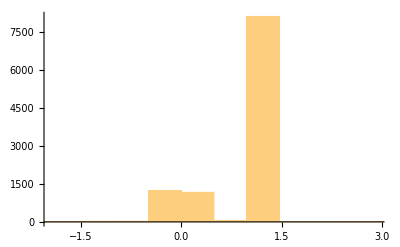

```mathematica
Histogram[Flatten[diffs]]
```

### Now I'm going to look more closely at the instances where they differ:

```mathematica
thresh = 0.99;
threshAbs = 1000;
Baddies = Table[Length[Select[diffs[[1;;100, i]], # > thresh|| # < -thresh &]], {i, 3^2 * 4}];
```

How many times does a particular location in the output deviate significantly?

```mathematica
Max[Baddies] // Print
ones = Flatten[Position[Flatten[diffs], _?(# == 1&)]];
Min[Flatten[diffsAbs][[ones]]]
Max[Flatten[diffsAbs][[ones]]]
```

78

-2.0977×10^7

2.05544×10^7

Positions where any diffs fail (is > `thresh` or < ` - thresh`):

```mathematica
badInds = DeleteDuplicates[Flatten[Table[Flatten[Position[diffs[[1;;100, iii]], _?(# > thresh || # < -thresh&)]], {iii, Length[diffs[[1]]]}]]]; 
badIndsAbs = DeleteDuplicates[Flatten[Table[Flatten[Position[diffsAbs[[1;;100, iii]], _?(# > threshAbs || # < -threshAbs&)]], {iii, Length[diffsAbs[[1]]]}]]]; 
oneInds = DeleteDuplicates[Flatten[Table[Flatten[Position[diffs[[1;;100, iii]], _?(# == 1&)]], {iii, Length[diffs[[1]]]}]]]; 
badIndsAbs //Print
badInds // Print
```

{28,99,20,45,53,91,44,93,61}

{1,2,3,4,6,7,8,9,10,11,12,13,15,16,17,19,20,21,23,24,26,27,29,30,32,33,35,36,37,38,39,40,41,42,43,44,45,46,47,48,52,53,54,55,56,57,58,59,60,61,64,65,67,68,69,70,72,73,75,76,77,81,83,84,85,88,89,92,93,94,95,96,98,99,100,22,82,91,78,28,31,62,71,49,51,86,5,14,18,66,79,80,87,90,25,34,50,63,74,97}

When they differ, how much do they differ by?

```mathematica
(* Table[Select[diffs[[i]], # > thresh|| # < -thresh&], {i, badInds}] // Print *)
```

Positions in the output that differ. Do any positions appear regularly?

```mathematica
(* Table[Flatten[Position[diffs[[i]], _?(# > thresh|| # < -thresh&)]], {i, badInds}] // Print *)
```

### Do analytical and numerical methods separately and compare to version in R:

```mathematica
badSeeds = seeds[[badInds]];
badSeedsAbs = seeds[[badIndsAbs]];
```

```mathematica
xseed = badSeedsAbs[[2]];
xn = 4;
xq = 3;
xsigma2 = 0.01;
SeedRandom[xseed];
xV = Table[RandomVariate[NormalDistribution[0,5],xq], {iii, xn}] ;
xN = Exp[RandomVariate[NormalDistribution[Log[10],0.5],xn]];
xf= Exp[RandomVariate[NormalDistribution[Log[0.2],0.5],1]][[1]];
xg=Exp[RandomVariate[NormalDistribution[Log[0.1],0.5],1]][[1]];
xeta = RandomVariate[NormalDistribution[0,0.1],1][[1]];
xCC = Table[xeta, {iii, xq}, {iii, xq}];
Do[xCC[[iii,iii]] = 1,{iii,xq}];
xCCC = xCC + Transpose[xCC];
xr0 = Exp[RandomVariate[NormalDistribution[Log[0.25],0.25],1]][[1]];
xd = RandomVariate[NormalDistribution[0,0.2],1][[1]];

xi = 1;
xinds = Drop[Table[j, {j, xn}], {xi}];

X = Table[Flatten[getXX[xV, xN, xd,xf, xg, xr0, xCCC, xsigma2, xi, k]] , {k, xinds}];
Y = Table[Flatten[getYY[xV, xN, xd,xf, xg, xr0, xCCC, xsigma2, xi, k]] , {k, xinds}];

Z = (X - Y) / X;
bi = Flatten[Position[Z, _?(# > thresh|| # < -thresh&)]]
ArrayReshape[X[[1]], {xq, xq}]
ArrayReshape[Y[[1]], {xq, xq}]
```

{1,1,1,2,1,3,1,7,1,8,1,9,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9}

{{-20359.4,12380.6,-57581.},{45126.1,-27441.4,127627.},{80163.7,-48747.8,226721.}}

{{-131.3,65.2422,-133054.},{64153.1,-30956.6,123826.},{-342342.,155762.,-623047.}}

```mathematica
X
Y
```

{{-20359.4,12380.6,-57581.,45126.1,-27441.4,127627.,80163.7,-48747.8,226721.},{-0.0666942,0.040557,-0.188626,-0.142146,0.0864396,-0.402021,0.195343,-0.118789,0.552475},{-1.44947×10^20,8.8143×10^19,-4.09944×10^20,4.17922×10^19,-2.5414×10^19,1.18198×10^20,8.14152×10^19,-4.95089×10^19,2.30261×10^20}}

{{-131.3,65.2422,-133054.,64153.1,-30956.6,123826.,-342342.,155762.,-623047.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.45272×10^20,8.83407×10^19,-4.10863×10^20,4.17922×10^19,-2.5414×10^19,1.18198×10^20,8.14151×10^19,-4.95089×10^19,2.3026×10^20}}

```mathematica
(*
X[[bi]]
Y[[bi]]
*)
```

```mathematica
Print[InputForm[xV]]
Print[InputForm[xN]]
Print[InputForm[xd]]
Print[InputForm[xf]]
Print[InputForm[xg]]
Print[InputForm[xeta]]
```

{{-1.035135226826545, 0.6294695789187386, -2.9275973068212293}, {1.3871683674832844, -3.074626596462943, -5.461878602265369}, {1.0869232779894977, 2.3165726367479786, -3.1835347901248094}, {8.641910299457635, -2.4916965856629427, -4.854061651674097}}

{13.656503949124152, 10.307808021728777, 25.915553076697318, 14.7712661286843}

-0.5425461662696425

0.1402489762085508

0.2829075432843719

-0.0940078167926852